# Fit parabolico dei dati Metodo dei Minimi Quadrati Riccardo Finotello

# Istruzioni

Il presente foglio di calcolo di Mathematica permette di calcolare un fit lineare dei dati inseriti da un file .dat contenente tre colonne in cui siano inseriti, nell’ordine, ascisse, ordinate, errore sulle ordinate.
Il file di input può contenere anche un’eventuale riga di intestazione dei dati, che verrà automaticamente ignorata dal programma.
Dopo aver inserito i dati nella sezione “Input dei dati” è sufficiente dare il comando “Evaluate Notebook” dal menù “Evaluation”. Il risultato dell’analisi viene salvato in file all’interno della cartella “Documenti”, recanti il nome dell’analisi (viene creata una cartella dal nome dell’esperienza). E’ possibile far eseguire più di un’analisi all’interno della stessa esperienza, posto di cambiare il nome del fit relativo (cioè il nome della sottocartella).

Per info:
Riccardo Finotello
riccardo.finotello@edu.unito.it

# Input dei dati

```mathematica
Clear["Global`*"] (*reset dell'intero Notebook*)
Needs["ErrorBarPlots`"](*pacchetto per barre d'errore*)
```

```mathematica
NomeEsperienza="EffettoHall";(*Nome della cartella principale ..\SpettroscopiaAlfa. Evitare gli spazi tra le parole. *)
NomeFit="MagnetoresistenzaTotale";(*nome della sottocartella ..\SpettroscopiaAlfa\NomeFit. Evitare gli spazi tra le parole. *)
InputFile="Desktop\\MagnetoresistenzaTotale.dat";(*Inserire il path del file: doppia barra \\ per separare i file oppure singola /*)
EtichettaAscissa="B" ;
UnitàMisuraAscissa="mT";(*inserire il carattere _ oppure Blank[] se non specificata*)
EtichettaOrdinata="R";
UnitàMisuraOrdinata="Ω";(*inserire il carattere _ oppure Blank[] se non specificata*)
```

# Analisi dei dati

### Input del file indicato

```mathematica
inputData=Import[InputFile,"Data"];
Grid[inputData]
```

-262.822 | 52.5337 | 0.0740467
-230.022 | 52.3256 | 0.0738257
-176.477 | 52.0318 | 0.0735139
-159.988 | 51.9461 | 0.0734231
-139.776 | 51.8482 | 0.0733193
-123.11 | 51.787 | 0.0732545
-104.671 | 51.7136 | 0.0731768
-86.2316 | 51.6646 | 0.0731249
-69.5654 | 51.6157 | 0.0730731
-52.8992 | 51.5912 | 0.0730472
-32.5097 | 51.5545 | 0.0730084
-17.7938 | 51.5545 | 0.0730084
1 | 51.5912 | 0.0730472
19.7938 | 51.5789 | 0.0730343
36.46 | 51.5789 | 0.0730343
56.8495 | 51.6157 | 0.0730731
71.7427 | 51.6401 | 0.073099
90.3592 | 51.6769 | 0.0731379
107.025 | 51.7258 | 0.0731897
123.692 | 51.787 | 0.0732545
144.258 | 51.8727 | 0.0733453
158.974 | 51.9339 | 0.0734101
175.641 | 52.0073 | 0.073488
230.958 | 52.3501 | 0.0738516
264.468 | 52.5337 | 0.0740467

### Costruzione liste di ascisse, ordinate ed errori

```mathematica
If[StringQ[inputData[[1,1]]],ascissa=Drop[Flatten[inputData[[All,1]]],1],ascissa=Flatten[inputData[[All,1]]]];
If[StringQ[inputData[[1,2]]],ordinata=Drop[Flatten[inputData[[All,2]]],1],ordinata=Flatten[inputData[[All,2]]]];
If[StringQ[inputData[[1,3]]],sigmaOrdinata=Drop[Flatten[inputData[[All,3]]],1],sigmaOrdinata=Flatten[inputData[[All,3]]]];
Lungh=Length[ascissa];
```

```mathematica
TopLimit=50;
If[Lungh≤TopLimit,Print["x = ",ascissa],"Liste troppo lunghe per essere visualizzate"]
If[Lungh≤TopLimit,Print["y = ",ordinata],"Liste troppo lunghe per essere visualizzate"]
If[Lungh≤TopLimit,Print["σ_y = ",sigmaOrdinata],"Liste troppo lunghe per essere visualizzate"]
```

x = {-262.822,-230.022,-176.477,-159.988,-139.776,-123.11,-104.671,-86.2316,-69.5654,-52.8992,-32.5097,-17.7938,1,19.7938,36.46,56.8495,71.7427,90.3592,107.025,123.692,144.258,158.974,175.641,230.958,264.468}

y = {52.5337,52.3256,52.0318,51.9461,51.8482,51.787,51.7136,51.6646,51.6157,51.5912,51.5545,51.5545,51.5912,51.5789,51.5789,51.6157,51.6401,51.6769,51.7258,51.787,51.8727,51.9339,52.0073,52.3501,52.5337}

σ_y = {0.0740467,0.0738257,0.0735139,0.0734231,0.0733193,0.0732545,0.0731768,0.0731249,0.0730731,0.0730472,0.0730084,0.0730084,0.0730472,0.0730343,0.0730343,0.0730731,0.073099,0.0731379,0.0731897,0.0732545,0.0733453,0.0734101,0.073488,0.0738516,0.0740467}

### Controllo dei dati

```mathematica
If[Lungh==Length[ordinata]&&Lungh==Length[sigmaOrdinata],"Le liste sono consistenti","Errore: controllare l'input"]
```

Le liste sono consistenti

### Calcolo del ChiQuadrato (Esp1 - Prof. Balestra)

```mathematica
matD={{Sum[1/(sigmaOrdinata[[i]])^2,{i,Lungh}],Sum[ascissa[[i]]/(sigmaOrdinata[[i]])^2,{i,Lungh}],Sum[(ascissa[[i]])^2/(sigmaOrdinata[[i]])^2,{i,Lungh}]},{Sum[ascissa[[i]]/(sigmaOrdinata[[i]])^2,{i,Lungh}],Sum[(ascissa[[i]])^2/(sigmaOrdinata[[i]])^2,{i,Lungh}],Sum[(ascissa[[i]])^3/(sigmaOrdinata[[i]])^2,{i,Lungh}]},{Sum[(ascissa[[i]])^2/(sigmaOrdinata[[i]])^2,{i,Lungh}],Sum[(ascissa[[i]])^3/(sigmaOrdinata[[i]])^2,{i,Lungh}],Sum[(ascissa[[i]])^4/(sigmaOrdinata[[i]])^2,{i,Lungh}]}}  
matDinver=Inverse[matD];
matB ={Sum[ordinata[[i]]/(sigmaOrdinata[[i]])^2,{i,Lungh}],Sum[(ascissa[[i]]*ordinata[[i]])/(sigmaOrdinata[[i]])^2,{i,Lungh}],Sum[((ascissa[[i]])^2*ordinata[[i]])/(sigmaOrdinata[[i]])^2,{i,Lungh}]};
matA = matDinver. matB;
Print["D = ",MatrixForm[matD]]
Print["D^-1 = ",MatrixForm[matDinver]]
Print["B = ",MatrixForm[matB]]
Print["A = ",MatrixForm[matA]]
```

{{4651.55,4681.5,8.96152×10^7},{4681.5,8.96152×10^7,1.64062×10^8},{8.96152×10^7,1.64062×10^8,3.71457×10^12}}

D = (4651.55 | 4681.5 | 8.96152×10^7
4681.5 | 8.96152×10^7 | 1.64062×10^8
8.96152×10^7 | 1.64062×10^8 | 3.71457×10^12)

D^-1 = (0.000401679 | -3.24291×10^-9 | -9.69049×10^-9
-3.24291×10^-9 | 1.11598×10^-8 | -4.1466×10^-13
-9.69049×10^-9 | -4.1466×10^-13 | 5.03015×10^-13)

B = (241136.
243933.
4.67399×10^9)

A = (51.5651
2.14228×10^-6
0.0000142609)

### Creazione dei grafici

```mathematica
dati=Table[{ascissa[[i]],ordinata[[i]]},{i,Lungh}];
If[Lungh≤TopLimit,Grid[dati],"Griglia troppo lunga per essere visualizzata"]
```

-262.822 | 52.5337
-230.022 | 52.3256
-176.477 | 52.0318
-159.988 | 51.9461
-139.776 | 51.8482
-123.11 | 51.787
-104.671 | 51.7136
-86.2316 | 51.6646
-69.5654 | 51.6157
-52.8992 | 51.5912
-32.5097 | 51.5545
-17.7938 | 51.5545
1 | 51.5912
19.7938 | 51.5789
36.46 | 51.5789
56.8495 | 51.6157
71.7427 | 51.6401
90.3592 | 51.6769
107.025 | 51.7258
123.692 | 51.787
144.258 | 51.8727
158.974 | 51.9339
175.641 | 52.0073
230.958 | 52.3501
264.468 | 52.5337

```mathematica
err=Table[{dati[[i]],ErrorBar[sigmaOrdinata[[i]]]},{i,Lungh}];
If[Lungh≤TopLimit,Grid[err],"Griglia troppo lunga per essere visualizzata"]
```

{-262.822,52.5337} | ErrorBar[0.0740467]
{-230.022,52.3256} | ErrorBar[0.0738257]
{-176.477,52.0318} | ErrorBar[0.0735139]
{-159.988,51.9461} | ErrorBar[0.0734231]
{-139.776,51.8482} | ErrorBar[0.0733193]
{-123.11,51.787} | ErrorBar[0.0732545]
{-104.671,51.7136} | ErrorBar[0.0731768]
{-86.2316,51.6646} | ErrorBar[0.0731249]
{-69.5654,51.6157} | ErrorBar[0.0730731]
{-52.8992,51.5912} | ErrorBar[0.0730472]
{-32.5097,51.5545} | ErrorBar[0.0730084]
{-17.7938,51.5545} | ErrorBar[0.0730084]
{1,51.5912} | ErrorBar[0.0730472]
{19.7938,51.5789} | ErrorBar[0.0730343]
{36.46,51.5789} | ErrorBar[0.0730343]
{56.8495,51.6157} | ErrorBar[0.0730731]
{71.7427,51.6401} | ErrorBar[0.073099]
{90.3592,51.6769} | ErrorBar[0.0731379]
{107.025,51.7258} | ErrorBar[0.0731897]
{123.692,51.787} | ErrorBar[0.0732545]
{144.258,51.8727} | ErrorBar[0.0733453]
{158.974,51.9339} | ErrorBar[0.0734101]
{175.641,52.0073} | ErrorBar[0.073488]
{230.958,52.3501} | ErrorBar[0.0738516]
{264.468,52.5337} | ErrorBar[0.0740467]

```mathematica
If[StringQ[UnitàMisuraAscissa],AscissaLabel=EtichettaAscissa<>" ["<>UnitàMisuraAscissa<>"]",AscissaLabel=EtichettaAscissa];
If[StringQ[UnitàMisuraOrdinata],OrdinataLabel=EtichettaOrdinata<>" ["<>UnitàMisuraOrdinata<>"]",OrdinataLabel=EtichettaOrdinata];
```

### Grafici e parametri del primo fit

#### Grafico dei punti sperimentali

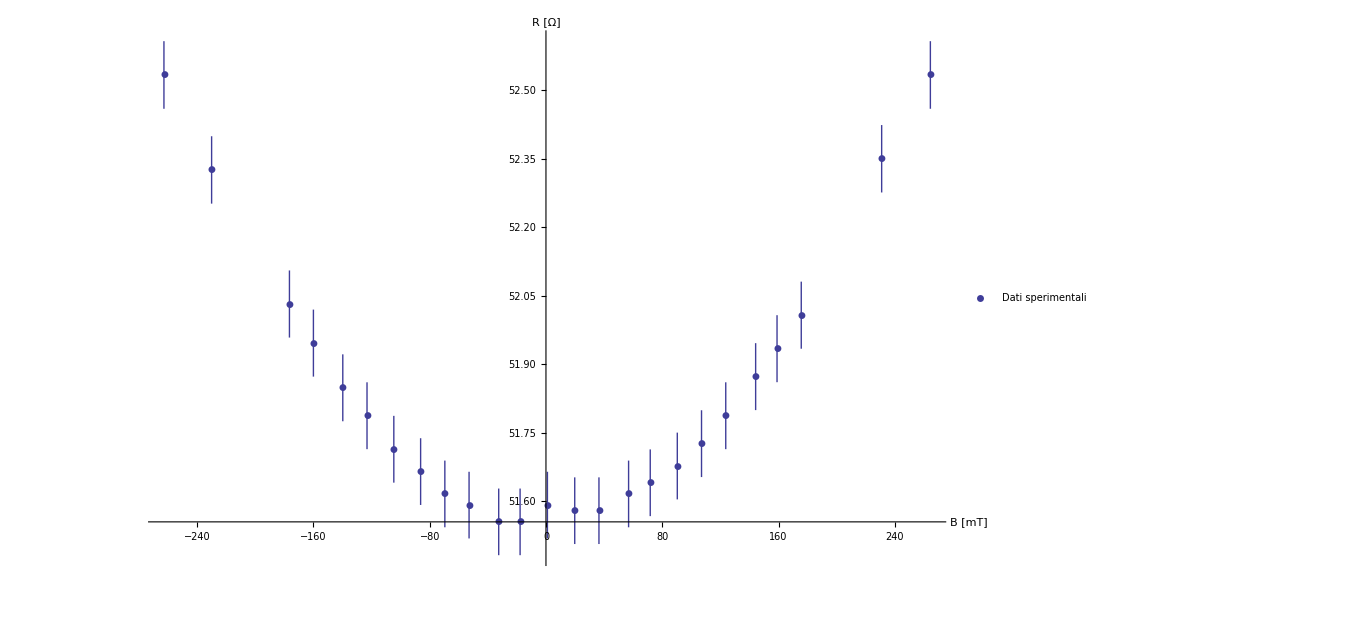

```mathematica
Grafico=ErrorListPlot[err,PlotRange->All,AxesLabel->{AscissaLabel,OrdinataLabel},LabelStyle->Directive[Black,Bold,Large],ImageSize->1000,PlotMarkers->Automatic,PlotLegends->{"Dati sperimentali"}]
```

#### Parametri del fit lineare con il metodo dei minimi quadrati

```mathematica
a=matA[[1]];
siga=Sqrt[matDinver[[1,1]]];
b=matA[[2]];
sigb=Sqrt[matDinver[[2,2]]];
c=matA[[3]];
sigc=Sqrt[matDinver[[3,3]]];
f[x_]:=a+b*x+c*x*x;
Print["Parabola y = f(x) = a + bx + cx^2"]
Print["a = (",a," ± ",siga,")",If[StringQ[UnitàMisuraOrdinata],UnitàMisuraOrdinata,""]]
Print["b = (",b," ± ",sigb,")",If[StringQ[UnitàMisuraOrdinata],UnitàMisuraOrdinata<>If[StringQ[UnitàMisuraAscissa],UnitàMisuraAscissa^-1,""],If[StringQ[UnitàMisuraAscissa],UnitàMisuraAscissa^-1,""]]]
Print["c = (",c," ± ",sigc,")",If[StringQ[UnitàMisuraOrdinata],UnitàMisuraOrdinata<>If[StringQ[UnitàMisuraAscissa],UnitàMisuraAscissa^-2,""],If[StringQ[UnitàMisuraAscissa],UnitàMisuraAscissa^-2,""]]]
```

Parabola y = f(x) = a + bx + cx^2

a = (51.5651 ± 0.0200419)Ω

StringJoin::string: String expected at position 2 in "\[CapitalOmega]" <> 1/"mT".

b = (2.14228×10^-6 ± 0.00010564)Ω<>1/mT

StringJoin::string: String expected at position 2 in "\[CapitalOmega]" <> 1/"mT"^2.

c = (0.0000142609 ± 7.09235×10^-7)Ω<>1/mT^2

#### Grafico della retta di fit

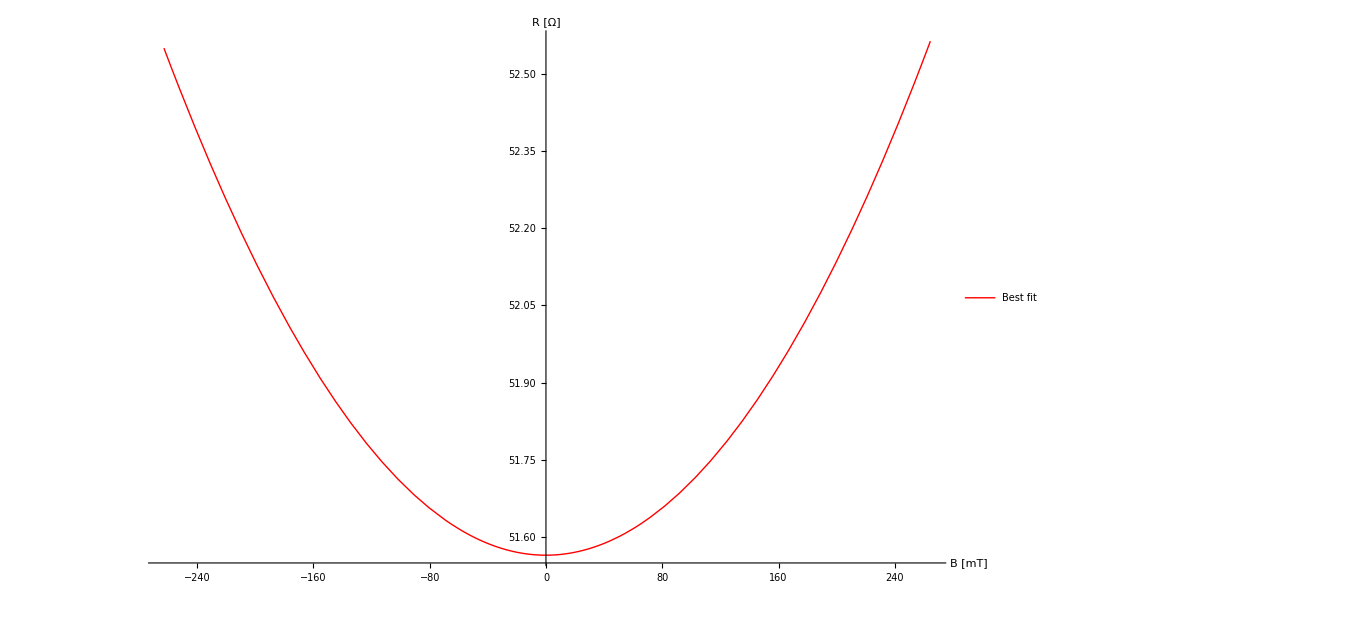

```mathematica
GraficoParabola=Plot[f[x],{x,First[ascissa],Last[ascissa]},PlotRange->All,ImageSize->1000,AxesLabel->{AscissaLabel,OrdinataLabel},LabelStyle->Directive[Black,Bold,Large],PlotStyle->Red,PlotLegends->{"Best fit"}]
```

#### Grafico cumulativo (dati e retta)

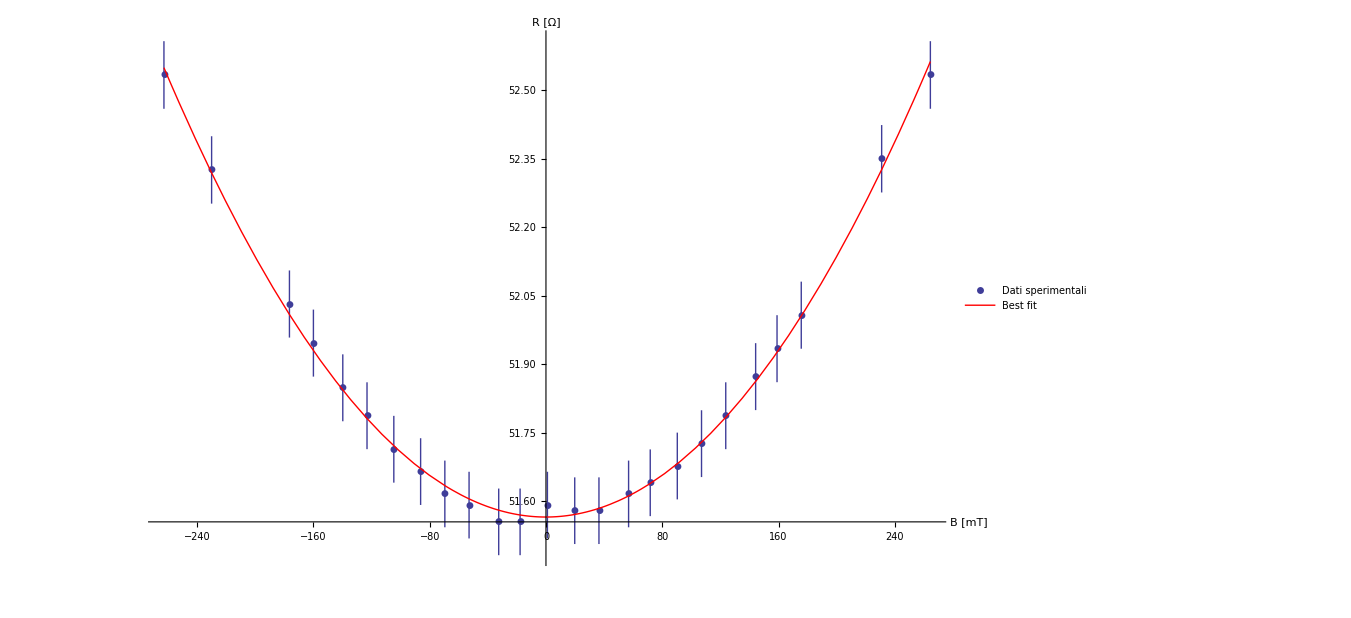

```mathematica
GraficoTot=Show[Grafico,GraficoParabola]
```

#### Parametri del Chi Quadro

```mathematica
chi2=Sum[(f[ascissa[[i]]]-ordinata[[i]])^2/sigmaOrdinata[[i]]^2,{i,Lungh}];
sy=Sqrt[Sum[(f[ascissa[[i]]]-ordinata[[i]])^2/(Lungh-3),{i,Lungh}]];
Print["Coefficiente di correlazione lineare: ρ = ",Correlation[ascissa,ordinata]] (*inserito per confronto con una distribuzione lineare*)
Print["χ^2 = ",chi2]
Print["Gradi di libertà del sistema: dof = ",Lungh-3]
Print["Eventuale errore a posteriori sulle ordinate: σ_y = ",sy,If[StringQ[UnitàMisuraOrdinata],UnitàMisuraOrdinata,""]]
```

Coefficiente di correlazione lineare: ρ = 0.00649328

χ^2 = 0.946815

Gradi di libertà del sistema: dof = 22

Eventuale errore a posteriori sulle ordinate: σ_y = 0.0152351Ω

# Export su file

```mathematica
CreateDirectory[$UserDocumentsDirectory<>"\\"<>NomeEsperienza<>"\\"<>NomeFit];
dir=$UserDocumentsDirectory<>"\\"<>NomeEsperienza<>"\\"<>NomeFit;
```

CreateDirectory::filex: "C:\\Users\\ricca_000\\Documents\\EffettoHall\\MagnetoresistenzaTotale\\" already exists.

```mathematica
If[DirectoryQ[dir<>"\\Analisi"],Analisi=SetDirectory[dir<>"\\Analisi"],Analisi=CreateDirectory[dir<>"\\Analisi"]];
SetDirectory[dir];
Print["I file verranno inseriti nelle cartelle corrispondenti al seguente indirizzo: ",dir]
```

I file verranno inseriti nelle cartelle corrispondenti al seguente indirizzo: C:\Users\ricca_000\Documents\EffettoHall\MagnetoresistenzaTotale

#### Export dei contenuti dell’analisi

```mathematica
outputAnalisi={{,"Analisi dati (errori sulle ordinate)",},{,,},{,"Parametri del fit (y = a + bx + cx^2)",},{"Parametro","Errore","Unità"},{"a = ",a,siga,If[StringQ[UnitàMisuraOrdinata],UnitàMisuraOrdinata,""]},{"b = ",b,sigb,If[StringQ[UnitàMisuraOrdinata],UnitàMisuraOrdinata<>If[StringQ[UnitàMisuraAscissa],UnitàMisuraAscissa<>"^(-1)",""],If[StringQ[UnitàMisuraAscissa],UnitàMisuraAscissa<>"^(-1)",""]]},{"c = ",c,sigc,If[StringQ[UnitàMisuraOrdinata],UnitàMisuraOrdinata<>If[StringQ[UnitàMisuraAscissa],UnitàMisuraAscissa<>"^(-2)",""],If[StringQ[UnitàMisuraAscissa],UnitàMisuraAscissa<>"^(-2)",""]]},{,,},{,"Coefficiente di correlazione lineare",},{"r = ",Correlation[ascissa,ordinata],},{,,},{,"Chi Quadrato",},{"chi = ",chi2,},{,,},{,"Errore a posteriori",},{"sigma = ",sy,},{,,},{,"Gradi di libertà",},{"dof = ",Lungh-3,}};
Export[file1=Analisi<>"\\AnalisiDati.xls",outputAnalisi];
Export[graph11=Analisi<>"\\GraficoExp.png",Grafico];
Export[graph21=Analisi<>"\\GraficoParabola.png",GraficoParabola];
Export[graph31=Analisi<>"\\GraficoSovrapposto.png",GraficoTot];
SetDirectory[dir];
If[FileExistsQ[file1],"File salvato in: "<>file1,"Errore: controllare i parametri"]
If[FileExistsQ[graph11],"File salvato in: "<>graph11,"Errore: controllare i parametri"]
If[FileExistsQ[graph21],"File salvato in: "<>graph21,"Errore: controllare i parametri"]
If[FileExistsQ[graph31],"File salvato in: "<>graph31,"Errore: controllare i parametri"]
```

File salvato in: C:\Users\ricca_000\Documents\EffettoHall\MagnetoresistenzaTotale\Analisi\AnalisiDati.xls

File salvato in: C:\Users\ricca_000\Documents\EffettoHall\MagnetoresistenzaTotale\Analisi\GraficoExp.png

File salvato in: C:\Users\ricca_000\Documents\EffettoHall\MagnetoresistenzaTotale\Analisi\GraficoParabola.png

File salvato in: C:\Users\ricca_000\Documents\EffettoHall\MagnetoresistenzaTotale\Analisi\GraficoSovrapposto.png